# Caracterización de una Nueva Función de Densidad Bivariada: Propiedades y Estimación de Parámetros

## Función de Densidad Bivariada

```mathematica
(*Parámetros de prueba*){a1,b1,c1,d1}={2.2,2.2,2.2,2.2};
```

### Constante de Normalización

```mathematica
K[a_,b_,c_,d_]:=Beta[a,b]*Beta[c,d];
```

### Superficie de la función de densidad

```mathematica
f[x_,y_]:=1/K[a,b,c,d](x^(a-1)y^(b-1)(x+y)^(d-(a+b)))/(x+y+1)^(c+d);
```

```mathematica
Block[{a=a1,b=b1,c=c1,d=d1},Plot3D[f[x,y],{x,0,2},{y,0,3.6},PlotRange->{0,10^-1},AxesLabel->{Subscript[x, 1],Subscript[x, 2],Densidad},ColorFunction->"Rainbow",Boxed->False]]
```

-Graphics3D-

### Curvas de Nivel Para La Función De Densidad Conjunta

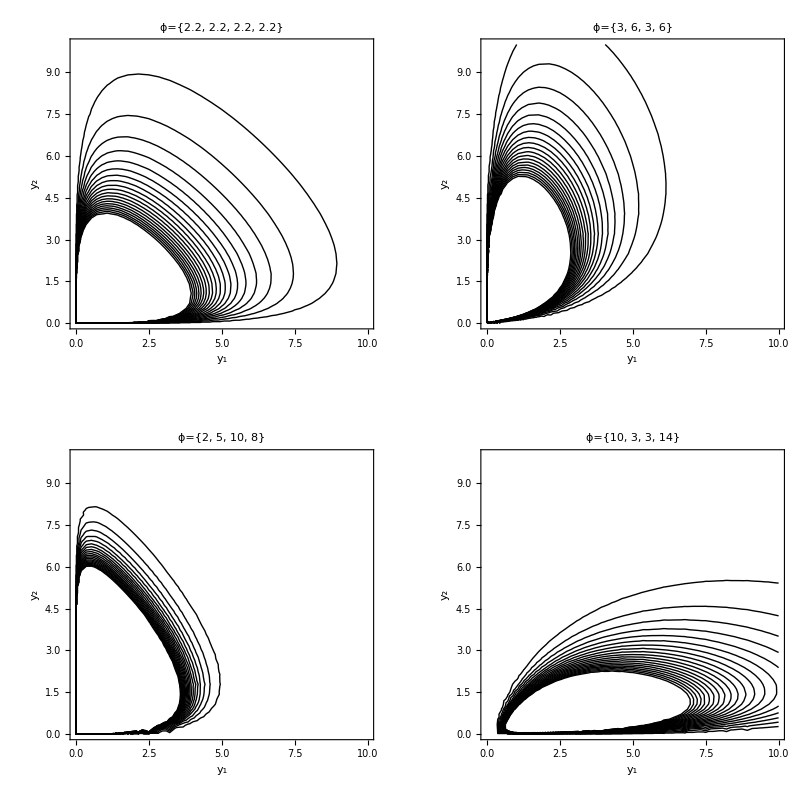

```mathematica
f[x_,y_,a_,b_,c_,d_]:=1/K[a,b,c,d] (x^(a-1) y^(b-1) (x+y)^(d-(a+b)))/(x+y+1)^(c+d)
(*Define los cuatro conjuntos de parámetros*)
params={{2.2,2.2,2.2,2.2},{3,6,3,6},{2,5,10,8},{10,3,3,14}};
(*Genera las curvas de nivel para cada conjunto de parámetros*)
contourPlots=ContourPlot[#,{x,0,10},{y,0,10},ContourShading->None,Contours->20,FrameLabel->{Subscript[y, 1],Subscript[y, 2]},PlotLabel->Style["ϕ="<>ToString[#2],10]]&@@@({f[x,y,##],{##}}&@@@params);
(*Organiza las gráficas en una cuadrícula*)
GraphicsGrid[Partition[contourPlots,2],Spacings->{20,20},Frame->All]
```

### Distribución de Probabilidad Acumulada Marginal para Y_1 (azul) y Y_2(roja)

```mathematica
ClearAll[Fx,Fy,generatePlotx,plots,generatePloty,combinedPlot];
LaunchKernels[7];
Fx[x_,a_,b_,c_,d_]:=N[Block[{a2=a,b2=b,c2=c,d2=d},x^d2/(d2 Beta[a2,b2] Beta[c2,d2])  NIntegrate[v^(-1-d2+a2) (1+v)^(d2-a2-b2)  Hypergeometric2F1[d2,c2+d2,1+d2,-((1+1/v) x)],{v,0,Infinity}]],3];
Fy[y_,a_,b_,c_,d_]:=N[Block[{a2=a,b2=b,c2=c,d2=d},y^d2/(d2 Beta[a2,b2] Beta[c2,d2])NIntegrate[v^(-1+a2) (1+v)^(d2-a2-b2) Hypergeometric2F1[d2,c2+d2,1+d2,-((1+v) y)],{v,0,Infinity}]],3];
DistributeDefinitions[Fx,Fy];
generatePlotx[a_,b_,c_,d_]:=Module[{pointsx,label},pointsx=ParallelTable[{x,Fx[x,a,b,c,d]},{x,0.1,12,0.1}];
label="ϕ = ("<>ToString[a]<>", "<>ToString[b]<>", "<>ToString[c]<>", "<>ToString[d]<>")";
ListPlot[pointsx,Joined->True,PlotRange->{{0,12},{0,1}},PlotLabel->label,PlotStyle->Blue]];
generatePloty[a_,b_,c_,d_]:=Module[{pointsy,label},pointsy=ParallelTable[{y,Fy[y,a,b,c,d]},{y,0.1,12,0.1}];
label="ϕ = ("<>ToString[a]<>", "<>ToString[b]<>", "<>ToString[c]<>", "<>ToString[d]<>")";
ListPlot[pointsy,Joined->True,PlotRange->{{0,12},{0,1}},PlotLabel->label,PlotStyle->Directive[Red,Dashed]]];
```

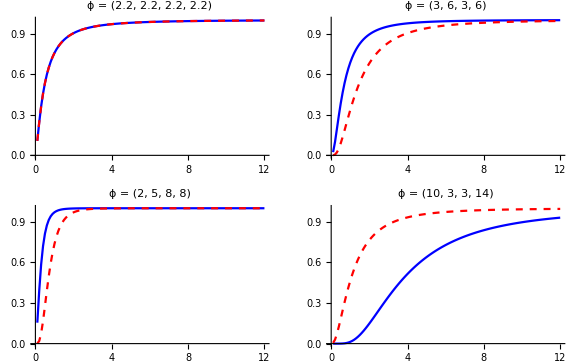

```mathematica
plots = {Show[generatePlotx[2.2, 2.2, 2.2, 2.2], generatePloty[2.2, 2.2, 2.2, 2.2]],
         Show[generatePlotx[3, 6, 3, 6], generatePloty[3, 6, 3, 6]],
         Show[generatePlotx[2, 5, 8, 8], generatePloty[2, 5, 8, 8]],
         Show[generatePlotx[10, 3, 3, 14], generatePloty[10, 3, 3, 14]]};
combinedPlot = GraphicsGrid[Partition[plots, 2], Spacings -> {20, 20}, 
  ImageSize -> Large]
(* Añadir la leyenda *)
Legended[combinedPlot, Placed[{"F(y_1)", "F(y_2)"}, Below]];
CloseKernels[];
```

### Función de Supervivencia

```mathematica
(*Parámetros de prueba*){a1,b1,c1,d1}={2.2,2.2,2.2,2.2};
```

```mathematica
S[x_,y_]:=N[Block[{a=a1,b=b1,c=c1,d=d1},1/(d Beta[a,b] Beta[c,d]) (y^d∫_(x/y)^∞ v^(-1+a) (1+v)^(d-a-b) Hypergeometric2F1[d,c+d,1+d,-((1+v) y)]ⅆv+x^d∫_0^∞ v^(-1-d+a) (1+v)^(d-a-b)  Hypergeometric2F1[d,c+d,1+d,-((1+1/v) x)]ⅆv)],3];
```

```mathematica
S[x_,y_]:=N[Block[{a=a1,b=b1,c=c1,d=d1},1-1/(d Beta[a,b] Beta[c,d]) (y^d NIntegrate[v^(-1+a) (1+v)^(d-a-b) Hypergeometric2F1[d,c+d,1+d,-((1+v) y)],{v,x/y,Infinity}]+x^d NIntegrate[v^(-1-d+a) (1+v)^(d-a-b)  Hypergeometric2F1[d,c+d,1+d,-((1+1/v) x)],{v,0,x/y}])],3];
```

```mathematica
Plot3D[S[x,y],{x,0.1,2},{y,0.1,2},PlotRange->{0,1},AxesLabel->{x,y,Supervivencia},ColorFunction->"Rainbow",Boxed->False]
```

-Graphics3D-

### Funciones de Densidad Marginal para Y_1 (azul) y Y_2(roja)

```mathematica
ClearAll[fx,fy,generatePlotx,plots,generatePloty,combinedPlot];
LaunchKernels[7];
fx[x_,a_,b_,c_,d_]:=N[Block[{a2=a,b2=b,c2=c,d2=d}, NIntegrate[ 1/(Beta[a2,b2] Beta[c2,d2])(x^(a2-1)y^(b2-1)(x+y)^(d2-(a2+b2)))/(x+y+1)^(c2+d2),{y,0,Infinity}]],3];
fy[y_,a_,b_,c_,d_]:=N[Block[{a2=a,b2=b,c2=c,d2=d}, NIntegrate[ 1/(Beta[a2,b2] Beta[c2,d2])(x^(a2-1)y^(b2-1)(x+y)^(d2-(a2+b2)))/(x+y+1)^(c2+d2),{x,0,Infinity}]],3];
DistributeDefinitions[fx,fy];
generatePlotx[a_,b_,c_,d_]:=Module[{pointsx,label},pointsx=ParallelTable[{x,fx[x,a,b,c,d]},{x,0.1,8,0.1}];
label="ϕ = ("<>ToString[a]<>", "<>ToString[b]<>", "<>ToString[c]<>", "<>ToString[d]<>")";
ListPlot[pointsx,Joined->True,PlotRange->{{0,8},{0,1.5}},PlotLabel->label,PlotStyle->Blue]];
generatePloty[a_,b_,c_,d_]:=Module[{pointsy,label},pointsy=ParallelTable[{y,fy[y,a,b,c,d]},{y,0.1,8,0.1}];
label="ϕ = ("<>ToString[a]<>", "<>ToString[b]<>", "<>ToString[c]<>", "<>ToString[d]<>")";
ListPlot[pointsy,Joined->True,PlotRange->{{0,8},{0,1.5}},PlotLabel->label,PlotStyle->Directive[Red,Dashed]]];
```

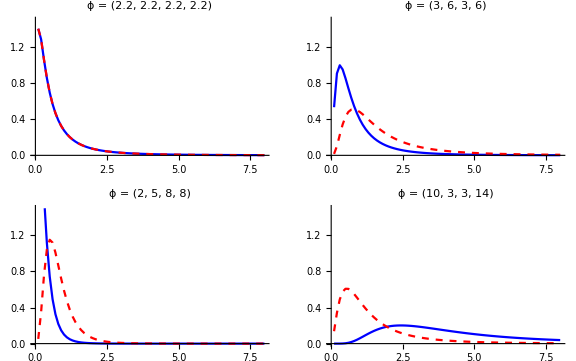

```mathematica
plots = {Show[generatePlotx[2.2, 2.2, 2.2, 2.2], generatePloty[2.2, 2.2, 2.2, 2.2]],
         Show[generatePlotx[3, 6, 3, 6], generatePloty[3, 6, 3, 6]],
         Show[generatePlotx[2, 5, 8, 8], generatePloty[2, 5, 8, 8]],
         Show[generatePlotx[10, 3, 3, 14], generatePloty[10, 3, 3, 14]]};
combinedPlot = GraphicsGrid[Partition[plots, 2], Spacings -> {20, 20}, 
  ImageSize -> Large]
CloseKernels[];
```

```mathematica
Export["/home/llerzy/Documentos/density.png",combinedPlot,"PNG"]
```

/home/llerzy/Documentos/density.png

### Momentos

```mathematica
(*Definir la función Mom para calcular los momentos*)Mom[m_,n_,a_,b_,c_,d_]:=Beta[c-m-n,m+n+d] Beta[m+a,n+b]/K[a,b,c,d];
(*Definir cada conjunto de parámetros*)
paramSets={{"{2.2, 2.2, 2.2, 2.2}",2.2,2.2,2.2,2.2},{"{3, 6, 3, 6}",3,6,3,6},{"{2, 5, 8, 8}",2,5,8,8},{"{10, 3, 3, 14}",10,3,3,14}};
(*Calcular y almacenar los resultados para cada conjunto de parámetros*)
results=Table[Module[{a=param[[2]],b=param[[3]],c=param[[4]],d=param[[5]],meanX,meanY,varianceX,varianceY,covarianceXY,moment2X,moment2Y},meanX=N[Mom[1,0,a,b,c,d]];(*Media de X*)meanY=N[Mom[0,1,a,b,c,d]];(*Media de Y*)moment2X=N[Mom[2,0,a,b,c,d]];(*Momento de segundo orden para X*)moment2Y=N[Mom[0,2,a,b,c,d]];(*Momento de segundo orden para Y*)covarianceXY=N[Mom[1,1,a,b,c,d]-Mom[1,0,a,b,c,d] Mom[0,1,a,b,c,d]];(*Covarianza*)varianceX=N[moment2X-meanX^2];(*Varianza de X*)varianceY=N[moment2Y-meanY^2];(*Varianza de Y*){param[[1]],meanX,meanY,varianceX,varianceY,covarianceXY}],{param,paramSets}];
(*Mostrar la tabla*)
TableForm[results,TableHeadings->{None,{"Configuración","E[X]","E[Y]","V[X]","V[Y]","Cov(X,Y)"}}]
```

Configuración | E[X] | E[Y] | V[X] | V[Y] | Cov(X,Y)
{2.2, 2.2, 2.2, 2.2} | 0.916667 | 0.916667 | 7.85108 | 7.85108 | 5.13503
{3, 6, 3, 6} | 1. | 2. | 1.8 | 5.8 | 2.2
{2, 5, 8, 8} | 0.326531 | 0.816327 | 0.0770512 | 0.251978 | 0.0395668
{10, 3, 3, 14} | 5.38462 | 1.61538 | 34.4675 | 4.31361 | 8.60947